```mathematica
Clear["Global`*"]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"solutions_and_parameters","plotstyle.m"}]];
Get[FileNameJoin[{NotebookDirectory[],"solutions_and_parameters","colors.m"}]];
Get[FileNameJoin[{NotebookDirectory[],"solutions_and_parameters","model_parameters.m"}]];
Get[FileNameJoin[{NotebookDirectory[],"solutions_and_parameters","solutions.m"}]];
```

```mathematica
x0v=0.4*λv;
wv=0.4*λv;
wCompv=0.8*λv;
Lv=4* λv;
```

## Two morhogen growth rule + feedback

Growth stops in any case, because the growth threshold at the middle (for symmetrical case) is reached. If the final source region width w is not zero at the growth arrest, that the thresholds for growth and feedback are connected with final parameters as follows.

```mathematica
SolutionSteadyRight[x_, x0_,  λ_, α_, w_, β_, Diff_, L_] := 2 α /(β Sinh[L/λ])  Sinh[w/(2 λ)] Cosh[(w + 2 x0)/(2 λ)] Cosh[(L - x)/λ] ;
```

#### Θgr = SolutionSteadyRight[Lfinal/2, x0final, λ, α, wComp - x0final, β, Diff, Lfinal]

```mathematica
SolutionSteadyRight[Lfinal/2, x0final,  λ, α, wComp - x0final, β, Diff, Lfinal]
```

(2 α Cosh[Lfinal/(2 λ)] Cosh[(wComp+x0final)/(2 λ)] Csch[Lfinal/λ] Sinh[(wComp-x0final)/(2 λ)])/β

#### Θfb = SolutionSteadyRight[Lfinal - x0final, x0final, λ, α, wComp - x0final, β, Diff, Lfinal]

```mathematica
SolutionSteadyRight[Lfinal - x0final, x0final,  λ, α, wComp - x0final, β, Diff, Lfinal]
```

(2 α Cosh[x0final/λ] Cosh[(wComp+x0final)/(2 λ)] Csch[Lfinal/λ] Sinh[(wComp-x0final)/(2 λ)])/β

```mathematica
Θgr[λ_,  α_, wComp_, β_, Diff_, Lfinal_, x0final_]:=(2 α Cosh[Lfinal/(2 λ)] Cosh[(wComp+x0final)/(2 λ)] Csch[Lfinal/λ] Sinh[(wComp-x0final)/(2 λ)])/β;
Θfb[λ_,  α_, wComp_, β_, Diff_, Lfinal_, x0final_]:=(2 α Cosh[x0final/λ] Cosh[(wComp+x0final)/(2 λ)] Csch[Lfinal/λ] Sinh[(wComp-x0final)/(2 λ)])/β
```

## x0final in [0, wComp], Lfinal in [wComp, +Inf]

Θgrv = 0.15841713400156207;
Θfbv = 0.6*Θgrv;

```mathematica
Θfbv = Θfb[λv,  αv, wCompv, βv, Diffv, Lv, 0]
```

0.0325434

```mathematica
Θgrv = 2.5*Θfbv;
```

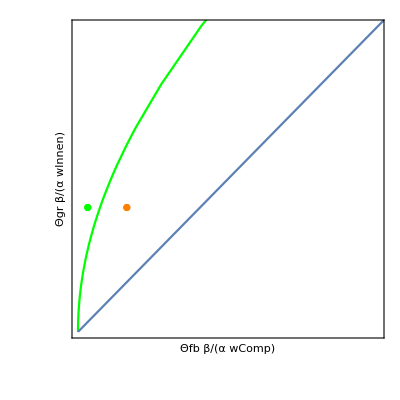

```mathematica
plotStyle[
Show[{
With[
{x0final=0},
ParametricPlot[
{
Θfb[λv,αv,wCompv,βv,Diffv,Lfinal,x0final]*(βv/(αv*wCompv)),
Θgr[λv,αv,wCompv,βv,Diffv,Lfinal,x0final]*(βv/(αv*wCompv))
},
{Lfinal,wCompv*2, 20*λv},
PlotStyle->Green, 
FrameLabel->{"Θfb β/(α wComp)","Θgr β/(α wInnen)"},
	AspectRatio -> 1/1,
	AxesOrigin->{0, 0},
	PlotRange->{{0,0.25}, {0,0.25}}
]
],
Plot[Θfb, {Θfb, 0, 1}],
ListPlot[{
{Θfbv*βv/(αv*wCompv), Θgrv*βv/(αv*wCompv)}
},
PlotStyle->Orange
],
ListPlot[{
{0.2*Θfbv*βv/(αv*wCompv), Θgrv*βv/(αv*wCompv)}
},
PlotStyle->Green
]
},
FrameTicks->None]]
```